```mathematica
(* 量子力学一维问题的Mahtematica演示 *)

(* ------------------------------------- Mahtematica基础------------------------------------------ *)
```

```mathematica
2;(*整数*)1/2;(*有理数*)0.5+I;(*复数*)E;(*自然常数*)Pi;(*圆周率*)
Abs[-2];(*绝对值*)
Re[1+I];(*复数的实部*)
Exp[3];(*指数函数*)
Sin[1];Cos[2];Cosh[3];Sinh[4];  (*三角函数与双曲函数*)
x=1;(*把1赋值给x*)
Solve[x+2==3,x];(*解关于x的方程*)
D[x^2,x];(*求导/求偏导*)
Integrate[x^2,x];(*不定积分/定积分*)
Clear[x];(*清除x的值和定义*)
Plot[x^2,{x,-1,2}]; (*画图*)
Manipulate[x^2,{x}];(*交互*)
f[x]=x^3;(*定义指定对象f[x]的值，x表示某一个具体对象*)
f[x_]:=x^3(*定义函数f[x]，x表示变量*)
```

```mathematica
(* ---------------------------------------- 自由粒子波函数-------------------------------------- *)

(* 平面波 *)

(* 简谐振动平面波在x处振动*)
(*参数预设,A为振幅，ω为振幅，v为速度*)
y[x_,t_,A_,ω_,v_]:=A*Cos[ω*x/v - ω *t];
Manipulate[Plot[y[x,t,A,ω,v],{x,0,5*Pi},Ticks->None,AxesLabel->{x}],{A},{ω},{v},{t,1,3,0.2}]
```

```mathematica
(* 自由粒子波包 *)
A=1/Sqrt[2*Pi*ℏ];
(* 原解析解 *)
(*c[k_] = A*Integrate[f[x]*E^(-I*k*x),{x,-Infinity,+Infinity}]； *)
(*ψ[x_,t_,m_]=Sqrt[ℏ/2/Pi]*Integrate[c[k]*E^(I*(k*x-k^2*ℏ*t/2/m)),{k,-Infinity,+Infinity}]； *)

(* 例题 *, 其中c、ψ为计算后的结果*)
f[x_]:=(1/Pi)^(1/4)*E^(-0.5*1*x^2); (* 以取f(x)高斯函数为例；*)
c[k_]:=1/Sqrt[ℏ] * (1/Pi)^(1/4)*E^(-0.5*k^2);
Φsquare[X_,τ_] := 1/Sqrt[Pi*(1+τ^2)]*E^(-X^2/(1+τ^2));
(*交互操作Φ[X_,τ_]^2*)
Manipulate[ Plot[Φsquare[X,τ],{X,-5,5},AxesLabel->{X,"|Φ[X,τ]|^2"},PlotRange->{0,0.6}],{τ,0,5,0.005}]
```

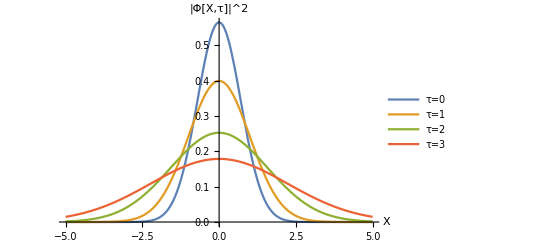

```mathematica
Plot[ {Φ[X,0],Φ[X,1],Φ[X,2],Φ[X,3]},{X,-5,5},AxesLabel->{X,"|Φ[X,τ]|^2"},PlotLegends->{"τ=0","τ=1","τ=2","τ=3"}]
```

```mathematica
ℏ = 6.62607015×10^(-34);
Width[t_,m_] := 2*Sqrt[1+(ℏ*t/m)^2];
Manipulate[Plot[Width[t,m] ,{t,0,1000}],{m}]
```

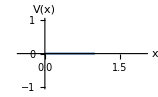

```mathematica
(* ---------------------------------------- 一维无限深势井-------------------------------- *)
Clear["Global`*"];(*Clear all variables*)

a= 1;(*参数预设*)

(* 一维无限深势井的绘制 *)

V := Piecewise[{ {Infinity,x≤0},{0, 0 < x<a},{Infinity,x≥a}}];
Plot[ {V},{x,-0.5,2(*这里与参数a有关*)},Ticks->None,AxesLabel->{x,"V(x)"}]
```

```mathematica
Clear[a];
(* k_n = n * Pi / a, n = 1, 2, 3... 的交互制作*)
k[n_,a_] := n * Pi / a;(* a是范围，这里也视为可以输入的参数*)
Manipulate[  k[n,a] ,{n},{a}]
```

```mathematica
(* 本征能量的交互制作*)
Eigenenergy[n_,m_,a_] := n^2 * Pi^2* ℏ ^2/ (2*m*a^2);
Manipulate[  Eigenenergy[n,m,a],{n},{a},{m}]
```

```mathematica
(* 本征函数的交互制作*)
ψ[n_,x_,a_] :=  Sin[n*Pi *x/a]*Sqrt[a/2];
(*交互图*)
Manipulate[ Plot[ ψ[n,x,a],{x,0,a},Ticks->None,AxesLabel->{x,ψ[n,x,a]}],{n,{1,2,3,4}},{a,1}]
```

```mathematica
(* 演示图*)
```

```mathematica
a = 1;
Plot[ {ψ[1,x,a],ψ[2,x,a],ψ[3,x,a]},{x,0,a},Ticks->None,AxesLabel->{"x/a","ψ_n(x)"},PlotLegends->{"n=1","n=2","n=3"}]
```

```mathematica
(* ---------------------------------------- 含时问题 ---------------------------------------- *)
```

```mathematica
Clear["Global`*"];(*Clear all variables*)
```

```mathematica
(*例题*)
f[x_] := Piecewise[{ {0,x≤0},{Sqrt[12]*x, 0 ≤  x<1/2},{Sqrt[12]*(1-x), 1/2<x≤1},{0,x≥1}}];
Plot[ f[x],{x,-0.5,1.5},AxesLabel->{x,"f(x)"}]
```

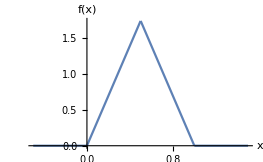

```mathematica
Ψ[x_,last_] := Sum[(8*Sqrt[3]/(n*Pi)^2)*Sin[n*Pi/2]*Sin[n*Pi*x],{n,last}];
Manipulate[Plot[Ψ[x,last],{x,0,1},PlotRange->{0,2}],{last,1,50,1}]
```

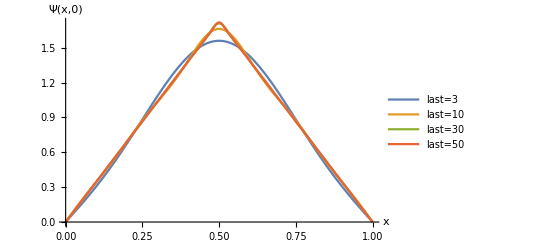

```mathematica
Plot[ {Ψ[x,3],Ψ[x,10],Ψ[x,30],Ψ[x,50]},{x,0,1},AxesLabel->{x,"Ψ(x,0)"},PlotLegends->{"last=3","last=10","last=30","last=50"}]
```

```mathematica
(* ---------------------------------------- 方形势垒 ------------------------------------ *)
Clear["Global`*"];(*Clear all variables*)
V := Piecewise[{ {0,x≤0},{1, 0 < x<1},{0,x≥1}}];
Plot[ V,{x,-0.3,2},Ticks->None,AxesLabel->{x,"V(x)"}]
```

```mathematica
(* E<V0时，投射系数 T *)
(* 为了方便 取 x= E/V0 *)
T[β_,x_ ]:=1/(1+1/(4*x(1-x))*Sinh[β*Sqrt[1-x]]^2);
Manipulate[ Plot[T[β,x],{x,0,1},AxesLabel->{"E/V0","T"},PlotRange->{0,1}],{β,2,0,-0.1}]
```

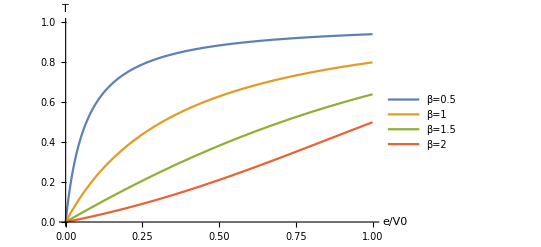

```mathematica
Plot[{T[0.5,x],T[1,x],T[1.5,x],T[2,x]},{x,0,1},AxesLabel->{e/V0,"T"},PlotRange->{0,1},Ticks->None,PlotLegends->{"β=0.5","β=1","β=1.5","β=2"}]
```

```mathematica
(* 概率密度的行为 *)
(*这里通过利用连续条件求通解中的系数*)
(* 取A = 1*)
k1=Sqrt[β^2 λ];k2=Sqrt[β^2(1-λ)];
sol=Solve[{1+B==C1,I k1/k2(1-B)==C2,C1 Cosh[k2]+C2 Sinh[k2]== D1 Exp[I k1],C1 Sinh[k2]+C2 Cosh[k2]== I k1/k2 D1 Exp[I k1]},{B,C1,C2,D1}];
(*简化成分段函数*)
ψsquare=Piecewise[{{1+Abs[B]^2+B *Exp[-2* I* k1* x]+Conjugate[B]*Exp[2*I*k1*x],-3 <=x<0},{Abs[C1]^2*Cosh[k2*x]^2+1/2 Sinh[2*k2*x]*(C1*Conjugate[C2]+C2*Conjugate[C1])+Abs[C2]^2*Sinh[k2*x]^2,0<=x<1},{Abs[D1]^2,x>=1}}];

Plot[( {ψsquare} /.sol/.{β->1.5,λ->0.5}),{x,-3,2},PlotRange->{0,4},PlotLegends->{"β=1.5"}]
Plot[( {ψsquare} /.sol/.{β->2,λ->0.5}),{x,-3,2},PlotRange->{0,4},PlotLegends->{"β=2"}]
```

```mathematica
(* E>V0时，投射系数 T *)
(* 为了方便 取 x= E/V0 *)
T[β_,x_ ]:=1/(1+1/(4*x(x-1))*Sin[β*Sqrt[x-1]]^2);
Manipulate[ Plot[T[β,x],{x,0,5},AxesLabel->{"E/V0","T"},PlotRange->{0,1}],{β,10,0,-0.1}]
```

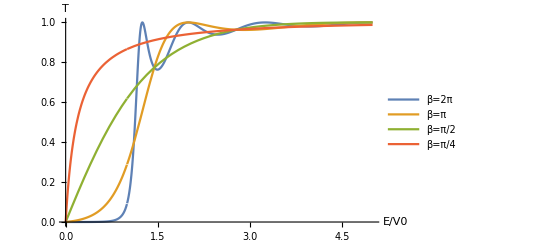

```mathematica
Plot[{T[2*Pi,x],T[Pi,x],T[Pi/2,x],T[Pi/4,x]},{x,0,5},AxesLabel->{"E/V0","T"},PlotRange->{0,1},Ticks->None,PlotLegends->{"β=2π","β=π","β=π/2","β=π/4"}]
```

```mathematica
(* ---------------------------------------- M形势垒 ------------------------------------ *)
```

```mathematica
Clear["Global`*"];(*Clear all variables*)
```

```mathematica
(*为画图方便，取V0 = 1, a = 2*)
V := Piecewise[{ {0,x≤0},{1-x, 0 < x<1},{x-1,1<x<2},{0,x>2}}];
Plot[ V,{x,-0.3,2.5},PlotRange->{0,1.3},Ticks->None,AxesLabel->{x,"V(x)"}]
```

```mathematica
(*电子穿过势垒*)
(*M形势垒电子的透射系数*)
m =0.51 10^6 ;  ℏ = 1;
(*V0=1 ;a=0.8 nm;*)
nm=1/197.3;
f=(2*V0)/a;
κ=((2*m*f)/ℏ^2)^(1/3);
k=(Sqrt[2*m*e]/ℏ);
ξ2=(-1*κ*e)/f;   ξ1=κ*(V0-e)/f;
c=AiryAi[ξ2];   c2=D[AiryAi[ξ],ξ]/.{ξ->ξ2};
d=AiryBi[ξ2];   d2=D[AiryBi[ξ],ξ]/.{ξ->ξ2};
u=AiryAi[ξ1];   u2=D[AiryAi[ξ],ξ]/.{ξ->ξ1};
σ=AiryBi[ξ1];   σ2=D[AiryBi[ξ],ξ]/.{ξ->ξ1};
α=κ*u2-I*k*u;
β=κ*σ2-I*k*σ;
T=1/Pi^4*(κ^2*k^2)/(Abs[c*c2*β^2+ d2*d*α^2-(c*d2+c2*d)*α*β]^2);

(*透射系数随着能量的变化情况*)
Plot[(T/.{V0->1,a->0.8/197.3}),{e,0,5},PlotRange->{0,1},AxesLabel->{"E/V0","T"}]
```

```mathematica
(*透射系数随势垒高度高度的变化*)
Plot[(T/.{e->1,a->0.8/197.3}),{V0,0,5},PlotRange->{0,1},AxesLabel->{"V0/E","T"}]
```

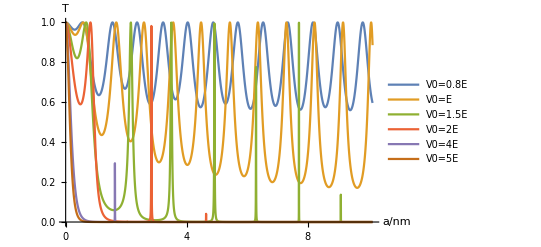

```mathematica
(*透射系数随着宽度的变化情况*)
Plot[{(T/.{e->1,V0->0.8}),(T/.{e->1,V0->1}),(T/.{e->1,V0->1.5}),(T/.{e->1,V0->2}),(T/.{e->1,V0->4}),(T/.{e->1,V0->5})},{a,0,10/197.3},PlotRange->{0,1},AxesLabel->{"a/nm","T"},Ticks->{  {   0,{0.01,2},{0.02,4},{0.03,6},{0.04,8},{0.05,10} },Automatic},PlotLegends->{"V0=0.8E","V0=E","V0=1.5E","V0=2E","V0=4E","V0=5E"}]
```

```mathematica
Clear["Global`*"];(*Clear all variables*)
c[V0_, a_]:=(1.6843052121898735*^8 (V0/a)^(2/3))/Abs[((0.-1009.9504938362078 ⅈ) AiryAi[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0]+126.82651410769991 (V0/a)^(1/3) AiryAiPrime[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0])^2 AiryBi[-(63.413257053849954 a (V0/a)^(1/3))/V0] AiryBiPrime[-(63.413257053849954 a (V0/a)^(1/3))/V0]-((0.-1009.9504938362078 ⅈ) AiryAi[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0]+126.82651410769991 (V0/a)^(1/3) AiryAiPrime[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0]) (AiryAiPrime[-(63.413257053849954 a (V0/a)^(1/3))/V0] AiryBi[-(63.413257053849954 a (V0/a)^(1/3))/V0]+AiryAi[-(63.413257053849954 a (V0/a)^(1/3))/V0] AiryBiPrime[-(63.413257053849954 a (V0/a)^(1/3))/V0]) ((0.-1009.9504938362078 ⅈ) AiryBi[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0]+126.82651410769991 (V0/a)^(1/3) AiryBiPrime[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0])+AiryAi[-(63.413257053849954 a (V0/a)^(1/3))/V0] AiryAiPrime[-(63.413257053849954 a (V0/a)^(1/3))/V0] ((0.-1009.9504938362078 ⅈ) AiryBi[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0]+126.82651410769991 (V0/a)^(1/3) AiryBiPrime[(63.413257053849954 a (-1+V0) (V0/a)^(1/3))/V0])^2]^2;

Manipulate[Plot[c[V0,a],{a,0,10/197.3},PlotRange->{0,1},AxesLabel->{"a/nm","T"},Ticks->{  {   0,{0.01,2},{0.02,4},{0.03,6},{0.04,8},{0.05,10} },Automatic}],{V0,0.5,5,0.1}]
```